# Blatt 6 - Jonas Neundorf & Jan Skottke

## Der “pill-box” Resonator

### Berechnung des allgemeinen elektrischen Feldes in der TM010 Mode

Lege einige Konstanten fest:

```mathematica
constants = {c -> 3.*10^8, q -> 1.602*10^-19};
```

Lege einen Ansatz fuer das E-Feld an:

```mathematica
e[r,t]:= e[r]*Cos[ω*t];
```

Stelle die Wellengleichung auf:

```mathematica
we=c^2*Laplacian[e[r,t],{r,θ,z},"Cylindrical"] == D[e[r,t],{t,2}]
```

c^2 ((Cos[t ω] e'[r])/r+Cos[t ω] e''[r])==-ω^2 Cos[t ω] e[r]

```mathematica
?Laplacian
```

RowBox[{"Laplacian", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["n", "TI"]]}], "}"}]}], "]"}] gives the Laplacian RowBox[{RowBox[{RowBox[{SuperscriptBox["∂", "2"], StyleBox["f", "TI"]}], "/", RowBox[{"∂", SuperscriptBox[SubscriptBox[StyleBox["x", "TI"], "1"], "2"]}]}], "+", StyleBox["…", "TR"], "+", RowBox[{RowBox[{SuperscriptBox["∂", "2"], StyleBox["f", "TI"]}], "/", RowBox[{"∂", SuperscriptBox[SubscriptBox[StyleBox["x", "TI"], StyleBox["n", "TI"]], "2"]}]}]}].
RowBox[{"Laplacian", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["n", "TI"]]}], "}"}], ",", StyleBox["chart", "TI"]}], "]"}] gives the Laplacian in the given coordinates StyleBox["chart", "TI"].

```mathematica
sol=DSolve[{we, e[0]== e0},e[r],r, Assumptions->{r ≤ R, -Infinity < e[r] < Infinity}]//Flatten
```

{e[r]→e0 BesselJ[0,(r ω)/c]}

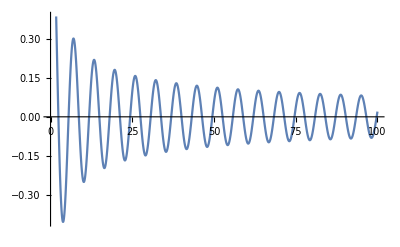

```mathematica
Plot[BesselJ[0, x], {x, 0, 100}]
```

```mathematica
Solve[e[r] == 0, {w}]
```

{}

```mathematica
?BesselJZero
```

RowBox[{"BesselJZero", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"]}], "]"}] represents the StyleBox["k", "TI"]SuperscriptBox["", "th"] zero of the Bessel function RowBox[{SubscriptBox[StyleBox["J", "TI"], StyleBox["n", "TI"]], "(", StyleBox["x", "TI"], ")"}].
RowBox[{"BesselJZero", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["k", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "]"}] represents the StyleBox["k", "TI"]SuperscriptBox["", "th"] zero greater than SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]].

```mathematica
ω -> c/R BesselJZero[0,1] //. constants
```

ω→(7.21448×10^8)/R